## 单层神经网络

```mathematica
net=DotPlusLayer[1,"Input"->"Scalar","Output"->"Scalar"];
```

```mathematica
net
```

DotPlusLayer[…]

```mathematica
trainingset = {1->1.9,2->4.1,3->6.0,4->8.1};
net=NetTrain[net,trainingset]
```

None

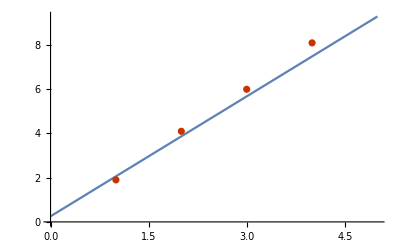

```mathematica
Show[{Plot[net[x],{x,0,5}],ListPlot[trainingset/.{Rule[x_,y_]:>{x,y}},PlotTheme->"Web"]}]
```

## 单因素分类问题

```mathematica
net=NetChain[{DotPlusLayer[2],SoftmaxLayer[]},
"Input"->"Scalar","Output"-> NetDecoder[{"Class",{False,True}}]];
```

```mathematica
net=NetTrain[net,{1->False,2->False,3->True,4->True}]
```

NetChain[]

```mathematica
in=Range[0,5];
Thread[in->net[in]]
```

{0→False,1→False,2→True,3→True,4→True,5→True}

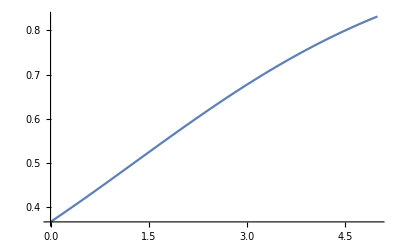

```mathematica
Plot[net[x,{"Probability",True}],{x,0,5}]
```

## 三层网络: (x,y)→x*y

```mathematica
net=NetChain[{32,Tanh,1},"Input"->2,"Output"->"Scalar"]
```

NetChain[]

```mathematica
trainingData=Flatten[Table[{x,y}->x*y,{x,-1,1,.005},{y,-1,1,.005}]];
```

```mathematica
net=NetTrain[net,trainingData,BatchSize->1024]
```

NetChain[]

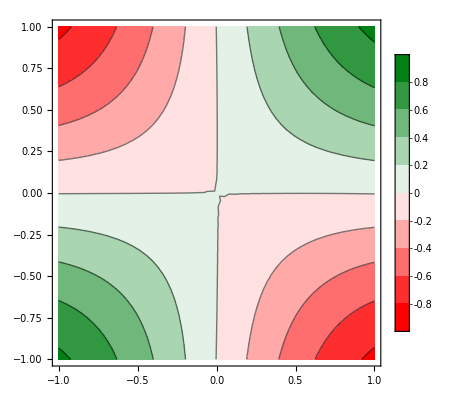

```mathematica
ContourPlot[net[{x,y}],{x,-1,1},{y,-1,1},ColorFunction->"RedGreenSplit",PlotLegends->Automatic
]
```

## 网络的可视化

```mathematica
net=NetTrain[NetGraph[{1,3,3,1},{1->2->3->4},"Input"->"Scalar","Output"->"Scalar"],{1->1.9,2->4.1,3->6.0,4->8.1}]
(*or
net=NetTrain[NetGraph[{1,3,3,1},{1->2->3->4},"Input"->"Scalar","Output"->"Scalar"],{1,2,3,4}->{1.9,4.1,6.,8.1}]
or
net=NetTrain[NetGraph[{1,3,3,1},{1->2->3->4},"Input"->"Scalar","Output"->"Scalar"],<|"Input"->{1,2,3,4},"Output"->{1.9,4.1,6.,8.1}|>]
*)
```

NetGraph[]

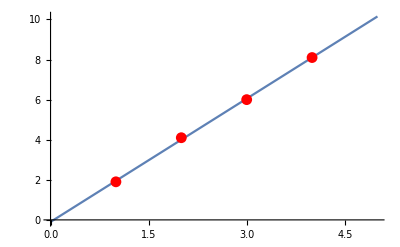

```mathematica
Show[{Plot[net[x],{x,0,5}],ListPlot[{1->1.9,2->4.1,3->6.0,4->8.1}/.{Rule[x_,y_]:>{x,y}},PlotTheme->"Minimal",PlotStyle->Red]}]
```

## 平均绝对误差层

```mathematica
net=DotPlusLayer["Input"->"Scalar","Output"->"Scalar"];
data={1->1.9,2->4.1,3->6.0,4->8.1};
trained=NetTrain[net,data]
```

None

```mathematica
trained[Range[4]]
```

{1.95001,4.,6.05,8.09999}

```mathematica
loss=MeanAbsoluteLossLayer["Target"->"Scalar"]
```

MeanAbsoluteLossLayer[…]

```mathematica
loss[<|"Input"->5.0,"Target"->3.0|>]
```

2.

```mathematica
trained=NetTrain[net,data,loss]
```

None

```mathematica
trained[Range[5]]
```

{1.90012,3.96677,6.03341,8.10006,10.1667}

## 用于比较两数大小的网络

```mathematica
net=NetChain[{2,SoftmaxLayer[]},"Input"->2,"Output"->NetDecoder[{"Class",{Less,Greater}}]]
```

NetChain[]

```mathematica
trained=NetTrain[net,{{1,2}->Less,{2,3}->Less,{4,2}->Greater,{3,1}->Greater}]
```

NetChain[]

```mathematica
trained[{{3,5},{5,3}}]
```

{Less,Greater}

```mathematica
loss=CrossEntropyLossLayer["Probabilities"]
```

CrossEntropyLossLayer[…]

```mathematica
trained=NetTrain[net,{{1,2}->{1.,0.},{2,3}->{1.,0.},{4,2}->{0.,1.},{3,1}->{0.,1.},{2,2}->{0.5,0.5},{3,3}->{0.5,0.5}},loss]
```

NetChain[]

```mathematica
trained[{{3,5},{5,3}}]
```

{Less,Greater}

```mathematica
net=DotPlusLayer["Input"->"Scalar","Output"->"Scalar"]
```

DotPlusLayer[…]

```mathematica
tnet=NetGraph[{net,MeanAbsoluteLossLayer["Target"->"Scalar"]},{1->2}]
```

NetGraph[]

```mathematica
data={1->1.9,2->4.1,3->6.0,4->8.1};
tnet=NetTrain[tnet,data]
```

NetGraph[]

```mathematica
trained=NetExtract[tnet,1]
```

None

```mathematica
trained[Range[5]]
```

{{1.89992},{3.96659},{6.03325},{8.09992},{10.1666}}

```mathematica
tnet=NetGraph[{3,Tanh,1,MeanAbsoluteLossLayer["Target"->"Scalar"],MeanSquaredLossLayer["Target"->"Scalar"]},{1->2->3->4,3->5,3->NetPort["Output"]},
"Input"->"Scalar","Output"->"Scalar"]
```

NetGraph[]

```mathematica
NetInitialize[tnet][<|"Input"->5,"Target"->3|>]
```

<|Output→1.4048,Loss1→1.5952,Loss2→2.54465|>

### 指定单个损失函数

```mathematica
trained=NetTrain[tnet,{1->1.9,2->4.1,3->6.0,4->8.1},"Loss1"]
```

NetGraph[]

### 指定多个损失函数

```mathematica
trained=NetTrain[tnet,{1->1.9,2->4.1,3->6.0,4->8.1},{"Loss1","Loss2"}]
```

NetGraph[]

```mathematica
trained=Take[trained,{NetPort["Input"],NetPort["Output"]}]
```

NetGraph[]

```mathematica
trained[Range[5]]
```

{1.89879,4.09898,5.99709,8.09849,9.85478}

## 增加训练批次, 提升训练速度

```mathematica
trainingData=RandomReal[1,{10000,4}]->RandomReal[1,{10000,4}];
net=NetChain[{DotPlusLayer[8],DotPlusLayer[4]},"Input"->4];
NetTrain[net,trainingData,BatchSize->512,MaxTrainingRounds->20]
```

NetChain[]

## 对每个训练数据指定训练次数

```mathematica
trainingData=RandomReal[1,{10000,4}]->RandomReal[1,{10000,4}];
net=NetChain[{8,4},"Input"->4];
NetTrain[net,trainingData,MaxTrainingRounds->1]
```

NetChain[]

## 指明梯度下降法作为训练方法

```mathematica
dotPlus=DotPlusLayer[1,"Input"->"Scalar","Output"->"Scalar"]
```

DotPlusLayer[…]

```mathematica
data={1->2.2,2->3.8,3->6.4,4->9.1};
```

```mathematica
net=NetTrain[dotPlus,data,Method->"StochasticGradientDescent"]
```

None

### 指定学习速率

```mathematica
net=NetTrain[dotPlus,data,Method->{"StochasticGradientDescent","InitialLearningRate"->0.1}]
```

None

### 动态学习速率

```mathematica
schedule[b_,bmax_,rate_]:=rate/(2-b/bmax);
net=NetTrain[dotPlus,data,Method->{"StochasticGradientDescent","LearningRateSchedule"->schedule}]
```

None

## 正则化权重, 预防过拟合.

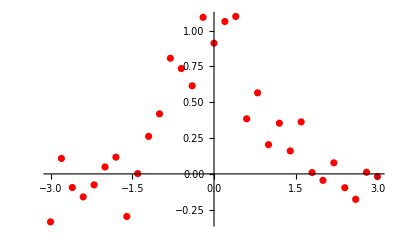

```mathematica
data=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];
plot=ListPlot[List@@@data,PlotStyle->Red]
```

```mathematica
net=NetChain[{150,Tanh,150,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net1=NetTrain[net,data,Method->"ADAM"];
```

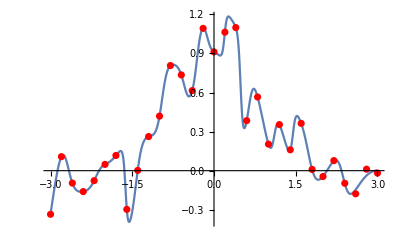

```mathematica
Show[Plot[net1[x],{x,-3,3}],plot]
```

```mathematica
net2=NetTrain[net,data,Method->{"ADAM","L2Regularization"->5}]
```

NetChain[]

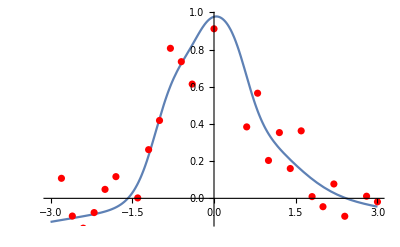

```mathematica
Show[Plot[net2[x],{x,-3,3}],plot]
```

## GPU训练网络(没有GPU驱动...)

```mathematica
trainingData=RandomReal[1,{10000,4}]->RandomReal[1,{10000,4}];
net=NetChain[{8,4},"Input"->4];
NetTrain[net,trainingData,TargetDevice->"GPU"]
```

Failure[…]

## 交叉验证, 防止过拟合

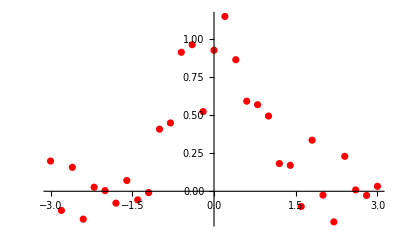

```mathematica
data=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];
plot=ListPlot[List@@@data,PlotStyle->Red]
```

```mathematica
net=NetChain[{150,Tanh,150,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net1=NetTrain[net,data,Method->"ADAM"];
```

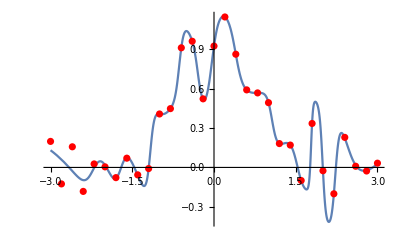

```mathematica
Show[Plot[net1[x],{x,-3,3}],plot]
```

```mathematica
data=RandomSample[data];
{train,test}=TakeDrop[data,24];
```

```mathematica
net2=NetTrain[net,train,ValidationSet->test];
```

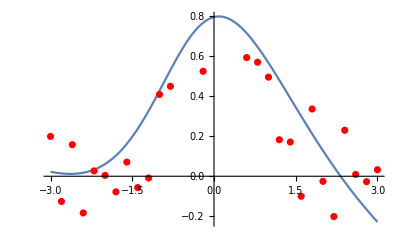

```mathematica
Show[Plot[net2[x],{x,-3,3}],plot]
```

## 聚类

```mathematica
sampledata[center_]:=RandomVariate[MultinormalDistribution[center,IdentityMatrix[2]],200];
clusters = sampledata/@ {{1.5,1}, {-1.5,1},{0,-3}};
```

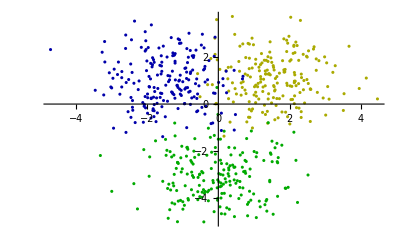

```mathematica
ListPlot[clusters, PlotStyle->Darker@{Yellow,Blue,Green}]
```

```mathematica
net=NetChain[{30,Ramp,3,SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{"a","b","c"}}]]
```

NetChain[]

```mathematica
trainingData=Join[Thread[clusters[[1]]->"a"],Thread[clusters[[2]]->"b"],Thread[clusters[[3]]->"c"]];
RandomSample[trainingData,10]
```

{{0.163081,-1.15246}→c,{0.687412,2.55462}→a,{0.750455,-2.85648}→c,{-2.60089,2.93212}→b,{1.71545,1.31302}→a,{1.29193,1.85996}→a,{-1.14298,-2.48029}→c,{2.06401,0.751004}→a,{-1.04286,0.582209}→b,{-1.08951,2.72836}→b}

```mathematica
trained=NetTrain[net,trainingData]
```

NetChain[]

```mathematica
Show[
Plot3D[{
trained[{x,y},{"Probability","a"}],trained[{x,y},{"Probability","b"}],trained[{x,y},{"Probability","c"}]
},{x,-4,4},{y,-5,4}, Exclusions->None],
ListPointPlot3D[Map[Append[#,1]&,clusters,{2}], PlotStyle->{Yellow,Blue,Green}]
]
```

-Graphics3D-

## Logistic

```mathematica
trainingData=ExampleData[{"MachineLearning","FisherIris"},"TrainingData"];
testData=ExampleData[{"MachineLearning","FisherIris"},"TestData"];
```

```mathematica
labels=Union[Values[trainingData]]
```

{setosa,versicolor,virginica}

```mathematica
net=NetChain[{3,SoftmaxLayer[]},"Input"->4,"Output"->NetDecoder[{"Class",labels}]]
```

NetChain[]

```mathematica
net=NetTrain[net,trainingData]
```

NetChain[]

### 混淆矩阵

```mathematica
cm=ClassifierMeasurements[net,testData];
```

```mathematica
cm["Accuracy"]
```

0.933333

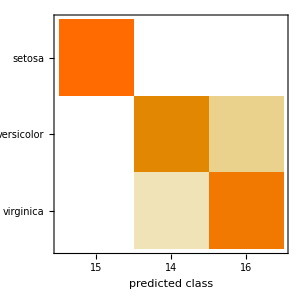

```mathematica
cm["ConfusionMatrixPlot"]
```

## 带有缺失自变量数据的网络训练

```mathematica
trainingData=ExampleData[{"MachineLearning","Titanic"},"TrainingData"];
testData=ExampleData[{"MachineLearning","Titanic"},"TestData"];
```

```mathematica
labels=Union[Values[trainingData]]
```

{died,survived}

```mathematica
classValues=DeleteDuplicates[trainingData[[All,1,1]]]
genderValues=DeleteDuplicates[trainingData[[All,1,3]]]
```

{1st,2nd,3rd}

{female,male}

```mathematica
encClass=NetEncoder[{"Class",classValues, "UnitVector"}]
encGender=NetEncoder[{"Class",genderValues,"UnitVector"}]
```

None

None

```mathematica
trainingData=DeleteMissing[trainingData,1,2];
testData=DeleteMissing[testData,1,2];
```

```mathematica
convertRow[{c_,a_,s_}->survived_]:=<|"class"-> c,"age"-> a,"sex"-> s,"survived"-> survived|>;
trainingDataset=Dataset[convertRow /@trainingData];
testDataset=Dataset[convertRow/@testData];
```

```mathematica
net=NetGraph[{CatenateLayer[],DotPlusLayer[2],SoftmaxLayer[]},{{NetPort["class"],NetPort["age"],NetPort["sex"]}->1,1->2->3->NetPort["survived"]},"class"-> encClass,"age"->"Scalar","sex"-> encGender,"survived"->NetDecoder[{"Class",labels}]]
```

NetGraph[]

```mathematica
net=NetTrain[net,trainingDataset,MaxTrainingRounds->400,BatchSize->256]
```

NetGraph[]

```mathematica
p[class_,age_,sex_]:=net[<|"class"->class,"age"->age,"sex"->sex|>,{"Probabilities","survived"}];
```

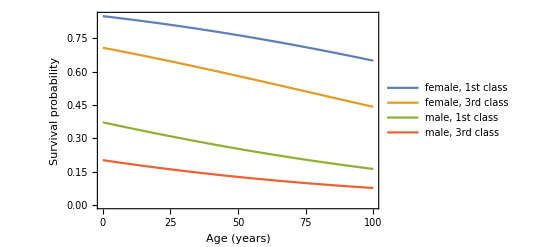

```mathematica
Plot[{p["1st",x,"female"],p["3rd",x,"female"],p["1st",x,"male"],p["3rd",x,"male"]}, {x,0,100},PlotLegends->{"female, 1st class", "female, 3rd class", "male, 1st class", "male, 3rd class"}, Frame->True,FrameLabel-> {"Age (years)", "Survival probability"}]
```

## 一维流形的学习, 豪夫曼编码

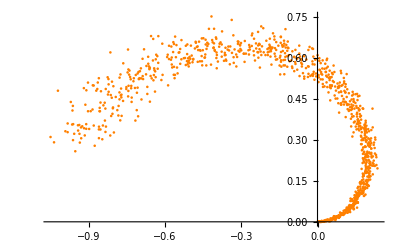

```mathematica
manifold=Table[AngleVector[{x,0.9Pi x}]+x/20*RandomVariate[NormalDistribution[],2],{x,0,1,0.001}];
plot=ListPlot[manifold,PlotStyle->Orange]
```

```mathematica
net=NetChain[{25,Ramp,1,25,Ramp,2},"Input"->2]
```

NetChain[]

```mathematica
lossNet=NetGraph[{net,MeanSquaredLossLayer[]},{1->2,NetPort["Input"]->NetPort[2,"Target"]}]
```

NetGraph[]

```mathematica
lossNet=NetTrain[lossNet,<|"Input"->manifold|>,BatchSize->4096];
trained=NetExtract[lossNet,1]
```

NetChain[]

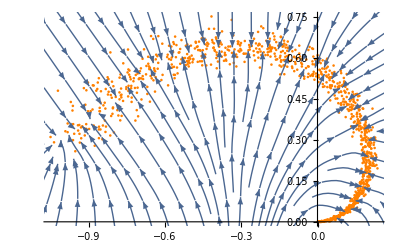

```mathematica
{{xmin,xmax},{ymin,ymax}}=CoordinateBounds[manifold,.2];
Show[plot,StreamPlot[trained[{x,y}]-{x,y},{x,xmin,xmax},{y,ymin,ymax}]]
```

```mathematica
decoder=Drop[trained,3]
encoder=Take[trained,3]
```

NetChain[]

NetChain[]

```mathematica
{min,max}=MinMax[encoder[manifold]]
```

{-0.196481,1.3576}

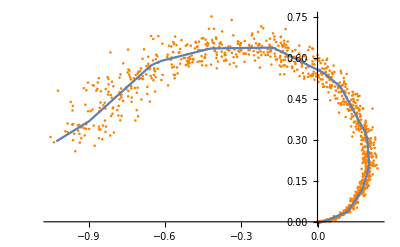

```mathematica
Show[plot,ListLinePlot[Table[decoder[x],{x,min,max,.01}]]]
```

## 无监督学习

```mathematica
resource = ResourceObject["MNIST"];
trainingData=ResourceData[resource,"TrainingData"];
testData=ResourceData[resource,"TestData"];
trainingSubset=Select[trainingData,Last[#]≤4&];
testSubset=Select[testData,Last[#]≤4&];
RandomSample[trainingSubset,8]
```

$Aborted

$Aborted

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,Last[#1]≤4&].

Select::normal: Nonatomic expression expected at position 1 in Select["1:eJzsvQd4FUX3+H/nTHrvIQmkAAkpdBCQGkCK9I4CUqR3CL1GVEREQEARRAUbCoiICIp0pAgihN4NHQw9BAiBsP+Z3b27U/a+f/N78qLv97mHh2T3frL17tmZOXNK3Kt…6InomJjmalryCrFLO+BwNUnp1WyP0B62664skBHh4RUy4ytoT7A9Lv5Jx+RMhshp6UBMYCOuLMgrAyZYxDTKS2bVET8KV6obYhPUIlTBIleoDBqNIVKz/+3y34/wCnAJGQ",«1»&].

RandomSample::lrwl: The set of items to sample from, Select[$Failed,Last[#1]≤4&], should be a non-empty list or a rule weights -> choices.

RandomSample[Select[$Failed,Last[#1]≤4&],8]

```mathematica
trainingImages=Keys[trainingSubset];
meanImage=Image[Mean@Map[ImageData,trainingImages]]
```

```mathematica
net=NetGraph[
{FlattenLayer[],50,Ramp,784,Tanh,ReshapeLayer[{1,28,28}],MeanSquaredLossLayer[]},
{1->2->3->4->5->6->NetPort["Output"],6->NetPort[7,"Input"],NetPort["Input"]->NetPort[7,"Target"]},
"Input"->NetEncoder[{"Image",{28,28},"Grayscale","MeanImage"->meanImage}],
"Output"->NetDecoder[{"Image","Grayscale"}]
]
```

```mathematica
trained=NetTrain[net,<|"Input"->trainingImages|>,"Loss"]
```

```mathematica
reconstructor=Take[trained,{NetPort["Input"],NetPort["Output"]}]
```

```mathematica
ImageAdd[reconstructor[#],meanImage]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
encoder=Take[trained,{NetPort["Input"],4}]
```

```mathematica
testImages = Keys[testSubset];
features = encoder[testImages];
```

```mathematica
components=ClusteringComponents[features,5,1];
Map[Part[testImages,RandomSample[#,10]]&,PositionIndex[components]]
```

```mathematica
representatives=Catenate@GroupBy[testSubset,Last->First,RandomSample[#,6]&];
ClusteringTree[encoder[representatives]->Map[ImageCrop,representatives]]
```

## 图像分类

```mathematica
resource = ResourceObject["MNIST"]
```

```mathematica
trainingData=ResourceData[resource,"TrainingData"];
testData=ResourceData[resource,"TestData"];
```

```mathematica
lenet=NetChain[{
ConvolutionLayer[20,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[50,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[10],
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",Range[0,9]}],
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

```mathematica
lenet=NetTrain[lenet,trainingData,ValidationSet->testData,MaxTrainingRounds-> 3]
```

```mathematica
imgs=Keys @ RandomSample[testData,5];
Thread[imgs->lenet[imgs]]
```

```mathematica
cm=ClassifierMeasurements[lenet,testData]
```

```mathematica
cm["Accuracy"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

## 图像识别

```mathematica
obj=ResourceObject["CIFAR-10"];
trainingData=ResourceData[obj,"TrainingData"];
RandomSample[trainingData,5]
```

```mathematica
classes=Union@Values[trainingData]
```

```mathematica
lenet=NetChain[
{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,10,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",classes}],
"Input"->NetEncoder[{"Image",{32,32}}]
]
```

```mathematica
trained=NetTrain[lenet,trainingData,MaxTrainingRounds->4]
```

```mathematica
trained[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

```mathematica
trained[-Graphics-,{"TopProbabilities",3}]
```

```mathematica
images=RandomSample[Keys[trainingData],5000];
```

```mathematica
entropies=trained[images,"Entropy"];
```

```mathematica
Labeled[images[[Ordering[entropies,-10]]],"high entropy"]
Labeled[images[[Ordering[entropies,10]]],"low entropy"]
```

## 多任务学习

```mathematica
obj=ResourceObject["CIFAR-100"]
```

```mathematica
trainingData=ResourceData[obj,"TrainingDataset"];
RandomSample[trainingData,5]
```

```mathematica
labels=Union@Normal@trainingData[All,"Label"]
```

```mathematica
sublabels=Union@Normal@trainingData[All,"SubLabel"]
```

```mathematica
convnet=NetChain[{
ConvolutionLayer[20,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[50,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp]
},"Input"->NetEncoder[{"Image",{32,32}}]]
```

```mathematica
net=NetGraph[{convnet,100,SoftmaxLayer[],20,SoftmaxLayer[]},{NetPort["Image"]->1->2->3->NetPort["SubLabel"],2->4->5->NetPort["Label"]},
"Label"->NetDecoder[{"Class",labels}],"SubLabel"->NetDecoder[{"Class",sublabels}]]
```

```mathematica
net=NetTrain[net,trainingData]
```

```mathematica
net[-Graphics-]
```

```mathematica
net[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"SubLabel"]
```

```mathematica
net[-Graphics-,"SubLabel"->{"TopProbabilities",3}]
```

```mathematica
images=RandomSample[Normal[trainingData][[All,"Image"]],5000];
```

```mathematica
entropies=net[images,"Label"->"Entropy"];
```

```mathematica
Labeled[images[[Ordering[entropies,-10]]],"high entropy"]
Labeled[images[[Ordering[entropies,10]]],"low entropy"]
```

```mathematica
subnet=Take[net,{NetPort["Image"],NetPort["SubLabel"]}]
```

```mathematica
subnet[-Graphics-]
```